```mathematica
<<"/Users/jpd/Development/Osaka/SXI/Schematic/gEDAmath.m"
```

```mathematica
fet[options___][refdes_]:=modeleqs[refdes,i["D"]==value(v["G"]-v["S"]),i["G"]==0,i["S"]+i["D"]==0]/.{options}/.{value->gm}
```

```mathematica
current[options___][refdes_]:={i[refdes,"1"]==value}/.{options}/.value->iin
```

```mathematica
<<"/Users/jpd/Development/Osaka/SXI/Schematic/parhimath.m"
```

```mathematica
tf=Simplify[transferFunction[in,out]]/.stim->0
```

(2 bw π (1+c2 r4 s) (gm (in+c1 in r1 s)+s (cgs in+c1 in (1+cgd r3 s+cgs (r1+r3) s))))/(in (2 bw π (gm (1+c2 r4 s) (1+c1 r1 s (1+cgd r3 s))+s (cgs+c2 cgs r4 s+c1 (1+cgd r3 s+cgs s (r1+r3+cgd r1 r3 s)+c2 s (r4 (1+cgd r3 s+cgs r3 s)+r1 (1+cgs (r3+r4) s+cgd r3 s (1+cgs r4 s))))))+s (gm (1+c2 r4 s) (1+cgd (r3+rout) s+c1 s (cgd r3 rout s+r1 (1+cgd (r3+rout) s)))+s (cgs (1+cgd (r3+rout) s)+c2 (1+cgs (r3+r4+rout) s+cgd (r3+rout) s (1+cgs r4 s))+c1 (1+cgd r3 s+cgd rout s+cgs s (r3+cgd r3 rout s+r1 (1+cgd (r3+rout) s))+c2 s (r4+rout+cgd r3 r4 s+cgs r3 r4 s+cgd r3 rout s+cgs r3 rout s+cgd r4 rout s+cgd cgs r3 r4 rout s^2+r1 (1+cgs (r3+r4+rout) s+cgd (r3+rout) s (1+cgs r4 s))))))))

```mathematica
tf/.s->0
```

1

```mathematica
zf=Simplify[transferFunction[-stim,out]]/.in->0
```

((1+c2 r4 s) (2 bw c1 π r1 s (1+cgd r3 s+cgs r3 s) stim+s (1+cgd r3 s+cgs r3 s+cgd rout s+cgs rout s+c1 s (rout (1+cgd r3 s+cgs r3 s)+r1 (1+cgd (r3+rout) s+cgs (r3+rout) s))) stim))/((2 bw π (gm (1+c2 r4 s) (1+c1 r1 s (1+cgd r3 s))+s (cgs+c2 cgs r4 s+c1 (1+cgd r3 s+cgs s (r1+r3+cgd r1 r3 s)+c2 s (r4 (1+cgd r3 s+cgs r3 s)+r1 (1+cgs (r3+r4) s+cgd r3 s (1+cgs r4 s))))))+s (gm (1+c2 r4 s) (1+cgd (r3+rout) s+c1 s (cgd r3 rout s+r1 (1+cgd (r3+rout) s)))+s (cgs (1+cgd (r3+rout) s)+c2 (1+cgs (r3+r4+rout) s+cgd (r3+rout) s (1+cgs r4 s))+c1 (1+cgd r3 s+cgd rout s+cgs s (r3+cgd r3 rout s+r1 (1+cgd (r3+rout) s))+c2 s (r4+rout+cgd r3 r4 s+cgs r3 r4 s+cgd r3 rout s+cgs r3 rout s+cgd r4 rout s+cgd cgs r3 r4 rout s^2+r1 (1+cgs (r3+r4+rout) s+cgd (r3+rout) s (1+cgs r4 s))))))) stim)

```mathematica
zf/.s->0
```

0

```mathematica
devpar={bw->0.2,rout->1.0,cgs->0.265,cgd->0}
```

{bw→0.2,rout→1.,cgs→0.265,cgd→0}

```mathematica
hicurr=(gm->2000Sqrt[0.1])
```

gm→632.456

```mathematica
natfreqs[p___]:=s/.Solve[Rationalize[Denominator[zf/.devpar/.{p}]]==0,s]
```

```mathematica
stability[z_]:=-Re[z]/Abs[z]
```

```mathematica
SetAttributes[stability,Listable]
```

```mathematica
natfreqs[hicurr,r1->0,r3->0,r4->0.0012,c2->10000,c1->0]
```

{-6.00073,-0.537604,-0.0928553}

```mathematica
stability[%]
```

{0.449773,0.449773,1.,1.}

```mathematica
locurr=(gm->2000Sqrt[0.001])
```

gm→63.2456

```mathematica
natfreqs[locurr,r1->0,r3->0,r4->0.0012,c2->10000,c1->0]
```

{-3.96185,-0.0474356-0.0728752 ⅈ,-0.0474356+0.0728752 ⅈ}

```mathematica
stability[%]
```

{1.,0.545528,0.545528}

```mathematica
Clear[nf]
nf[o_,r_,c_]:=(nf[o,r,c]=natfreqs[o,r1->10,r3->0,r4->r,c2->22000,c1->c])
```

```mathematica
nfh[r_,c_]:=nf[hicurr,r,c]
```

```mathematica
nfl[r_,c_]:= nf[locurr,r,c]
```

```mathematica
speed[r_?NumericQ,c_?NumericQ]:=Min@@-Re[nfh[r,c]]
```

```mathematica
speed[r_?NumericQ,c_?NumericQ]:=-Re[nfh[r,c][[3]]]
```

```mathematica
stab[r_?NumericQ,c_?NumericQ]:=Min@@stability[Join[nfl[r,c],nfh[r,c]]]
```

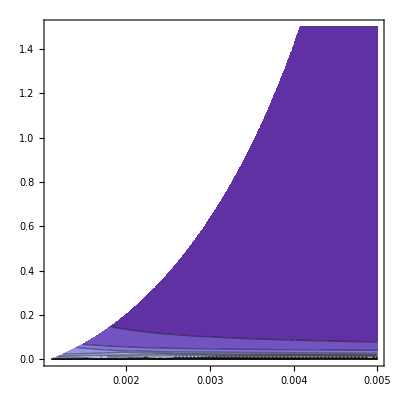

```mathematica
ContourPlot[speed[r4,c1],{r4,0.0,0.005},{c1,0.0,1.5},RegionFunction->Function[{r4,c1,z},stab[r4,c1]>0.5],PlotRange->All]
```

```mathematica
nfh[0.0033,0]
```

{-18722.2,-8.47891,-0.939617,-0.0138477}

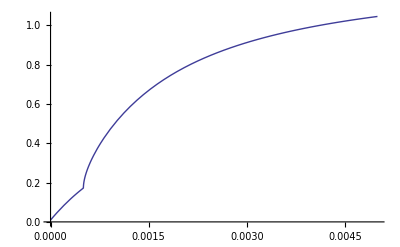

```mathematica
Plot[speed[r4,0],{r4,0,0.005}]
```

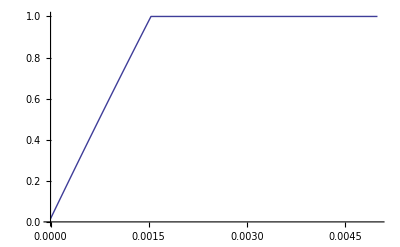

```mathematica
Plot[stab[r4,0],{r4,0,0.005}]
```

Bottom line :
  Eliminate, R1, C1, R3. 
  C2 -> 22 μF
R4 -> 1.8 ohm

Same parameters as low reg, although topology differs and behavior differs away from the sweet spot.